```mathematica
"path graph has paths as vertices and a direct edge from p1 to p2 iff p2 is a subpath of p1";
```

```mathematica
SubpathQ[p1_,p2_]:=If[IntersectingQ[p1,p2],
If[Length[p1]≤Length[p2],
If[SubsetQ[p2,p1],
¬StringFreeQ[StringDrop[StringDrop[ToString[p2],1],-1],StringDrop[StringDrop[ToString[p1],1],-1]]
,False],False],
False]
```

```mathematica
SubpathQ[p1_,p2_]:=¬StringFreeQ[StringDrop[StringDrop[ToString[p2],1],-1],StringDrop[StringDrop[ToString[p1],1],-1]]
SubpathQ2[p1_,p2_]:=(¬StringFreeQ[StringDrop[StringDrop[ToString[p2],1],-1],StringDrop[StringDrop[ToString[p1],1],-1]])&&(First[p1]==First[p2])
```

```mathematica
Block[{t=DeleteDuplicates[RandomInteger[10,5]]},
Block[{st=If[Length[t]>2,Delete[t,RandomInteger[{1,Length[t]}]],t]},
{SubpathQ[st,t],{t,st}}]]
```

{False,{{6,7,10,3,1},{6,7,3,1}}}

```mathematica
Delete[{1,2,3},2]
```

{1,3}

```mathematica
contrapairsQ[{a_,b_},{c_,d_}]:=a==d&&b==c
pairs[l_]:=Table[{l[[i]],l[[i+1]]},{i,1,Length[l]-1}]

ContradictingPathsQ[p1_,p2_]:=Block[{prs1=pairs[p1],prs2=pairs[p2],contra=False},
Do[If[contrapairsQ[prs1[[x]],prs2[[y]]],contra=True;Break[]],{x,1,Length[prs1]},{y,1,Length[prs2]}];contra]
```

```mathematica
ContradictingPathsQ[{1,2,3},{1,2,3,4,5}]
```

False

```mathematica
pairs[{1,2,3,4,5}]
```

{{1,2},{2,3},{3,4},{4,5}}

```mathematica
InterSubpathQ[p1_,p2_]:=If[SubsetQ[p2,p1],(p1==Select[p2,¬MemberQ[Complement[p2,p1],#]&])&&(First[p1]==First[p2])&&(Last[p1]==Last[p2]),False]
```

{4<->1,19<->1,20<->1,27<->1,33<->1,43<->1,44<->1,51<->1,54<->1,57<->1,60<->1,7<->2,21<->2,25<->2,26<->2,35<->2,45<->2,48<->2,49<->2,50<->2,58<->2,59<->2,10<->3,23<->3,29<->3,31<->3,32<->3,46<->3,47<->3,52<->3,53<->3,55<->3,56<->3,13<->4,14<->4,25<->4,31<->4,37<->4,38<->4,49<->4,53<->4,55<->4,59<->4,8<->5,15<->5,27<->5,28<->5,36<->5,39<->5,42<->5,51<->5,52<->5,56<->5,60<->5,11<->6,17<->6,30<->6,33<->6,34<->6,40<->6,41<->6,50<->6,54<->6,57<->6,58<->6,15<->7,16<->7,19<->7,32<->7,39<->7,40<->7,43<->7,47<->7,56<->7,57<->7,13<->8,21<->8,22<->8,34<->8,37<->8,41<->8,45<->8,46<->8,55<->8,58<->8,12<->9,18<->9,24<->9,35<->9,36<->9,38<->9,42<->9,44<->9,48<->9,59<->9,60<->9,17<->10,18<->10,20<->10,26<->10,41<->10,42<->10,44<->10,45<->10,50<->10,51<->10,14<->11,23<->11,24<->11,28<->11,38<->11,39<->11,47<->11,48<->11,49<->11,52<->11,16<->12,22<->12,29<->12,30<->12,37<->12,40<->12,43<->12,46<->12,53<->12,54<->12,15<->13,19<->13,20<->13,27<->13,28<->13,33<->13,36<->13,39<->13,42<->13,43<->13,44<->13,51<->13,52<->13,54<->13,56<->13,57<->13,60<->13,17<->14,19<->14,20<->14,27<->14,30<->14,33<->14,34<->14,40<->14,41<->14,43<->14,44<->14,50<->14,51<->14,54<->14,57<->14,58<->14,60<->14,21<->15,22<->15,25<->15,26<->15,34<->15,35<->15,37<->15,41<->15,45<->15,46<->15,48<->15,49<->15,50<->15,55<->15,58<->15,59<->15,18<->16,21<->16,24<->16,25<->16,26<->16,35<->16,36<->16,38<->16,42<->16,44<->16,45<->16,48<->16,49<->16,50<->16,58<->16,59<->16,60<->16,23<->17,24<->17,28<->17,29<->17,31<->17,32<->17,38<->17,39<->17,46<->17,47<->17,48<->17,49<->17,52<->17,53<->17,55<->17,56<->17,22<->18,23<->18,29<->18,30<->18,31<->18,32<->18,37<->18,40<->18,43<->18,46<->18,47<->18,52<->18,53<->18,54<->18,55<->18,56<->18,21<->19,25<->19,26<->19,31<->19,35<->19,37<->19,38<->19,45<->19,48<->19,49<->19,50<->19,53<->19,55<->19,58<->19,59<->19,23<->20,25<->20,29<->20,31<->20,32<->20,37<->20,38<->20,46<->20,47<->20,49<->20,52<->20,53<->20,55<->20,56<->20,59<->20,27<->21,28<->21,32<->21,36<->21,39<->21,40<->21,42<->21,43<->21,47<->21,51<->21,52<->21,56<->21,57<->21,60<->21,24<->22,27<->22,28<->22,35<->22,36<->22,38<->22,39<->22,42<->22,44<->22,48<->22,51<->22,52<->22,56<->22,59<->22,60<->22,26<->23,30<->23,33<->23,34<->23,40<->23,41<->23,42<->23,44<->23,45<->23,50<->23,51<->23,54<->23,57<->23,58<->23,29<->24,30<->24,33<->24,34<->24,37<->24,40<->24,41<->24,43<->24,46<->24,50<->24,53<->24,54<->24,57<->24,58<->24,27<->25,32<->25,33<->25,39<->25,40<->25,43<->25,44<->25,47<->25,51<->25,54<->25,56<->25,57<->25,60<->25,29<->26,31<->26,32<->26,39<->26,40<->26,43<->26,46<->26,47<->26,52<->26,53<->26,55<->26,56<->26,57<->26,31<->27,34<->27,37<->27,38<->27,41<->27,45<->27,46<->27,49<->27,53<->27,55<->27,58<->27,59<->27,30<->28,33<->28,34<->28,37<->28,40<->28,41<->28,45<->28,46<->28,50<->28,54<->28,55<->28,57<->28,58<->28,35<->29,36<->29,38<->29,41<->29,42<->29,44<->29,45<->29,48<->29,50<->29,51<->29,59<->29,60<->29,35<->30,36<->30,38<->30,39<->30,42<->30,44<->30,47<->30,48<->30,49<->30,52<->30,59<->30,60<->30,33<->31,41<->31,42<->31,43<->31,44<->31,45<->31,50<->31,51<->31,54<->31,57<->31,60<->31,35<->32,41<->32,42<->32,44<->32,45<->32,48<->32,49<->32,50<->32,51<->32,58<->32,59<->32,37<->33,38<->33,39<->33,47<->33,48<->33,49<->33,52<->33,53<->33,55<->33,59<->33,36<->34,38<->34,39<->34,42<->34,47<->34,48<->34,49<->34,51<->34,52<->34,56<->34,60<->34,37<->35,39<->35,40<->35,43<->35,46<->35,47<->35,53<->35,54<->35,56<->35,57<->35,37<->36,40<->36,41<->36,43<->36,45<->36,46<->36,53<->36,54<->36,55<->36,58<->36,38<->37,39<->37,42<->37,43<->37,44<->37,48<->37,51<->37,52<->37,54<->37,56<->37,57<->37,59<->37,60<->37,40<->38,41<->38,43<->38,44<->38,46<->38,50<->38,51<->38,53<->38,54<->38,57<->38,58<->38,60<->38,40<->39,41<->39,45<->39,46<->39,48<->39,49<->39,50<->39,54<->39,55<->39,57<->39,58<->39,59<->39,42<->40,44<->40,45<->40,47<->40,48<->40,49<->40,50<->40,52<->40,58<->40,59<->40,60<->40,42<->41,46<->41,47<->41,48<->41,49<->41,51<->41,52<->41,53<->41,55<->41,56<->41,60<->41,43<->42,45<->42,46<->42,47<->42,52<->42,53<->42,54<->42,55<->42,56<->42,58<->42,44<->43,45<->43,48<->43,49<->43,50<->43,53<->43,55<->43,58<->43,59<->43,60<->43,46<->44,47<->44,49<->44,52<->44,53<->44,54<->44,55<->44,56<->44,59<->44,46<->45,47<->45,51<->45,52<->45,53<->45,55<->45,56<->45,57<->45,60<->45,48<->46,50<->46,51<->46,52<->46,56<->46,59<->46,60<->46,48<->47,49<->47,50<->47,51<->47,54<->47,57<->47,58<->47,59<->47,50<->48,53<->48,54<->48,56<->48,57<->48,58<->48,50<->49,51<->49,54<->49,56<->49,57<->49,58<->49,60<->49,52<->50,53<->50,55<->50,56<->50,57<->50,52<->51,53<->51,55<->51,56<->51,58<->51,59<->51,54<->52,55<->52,57<->52,58<->52,54<->53,57<->53,59<->53,60<->53,55<->54,59<->54,60<->54,56<->55,57<->55,60<->55,58<->56,59<->56,58<->57,59<->57,60<->58,60<->59}

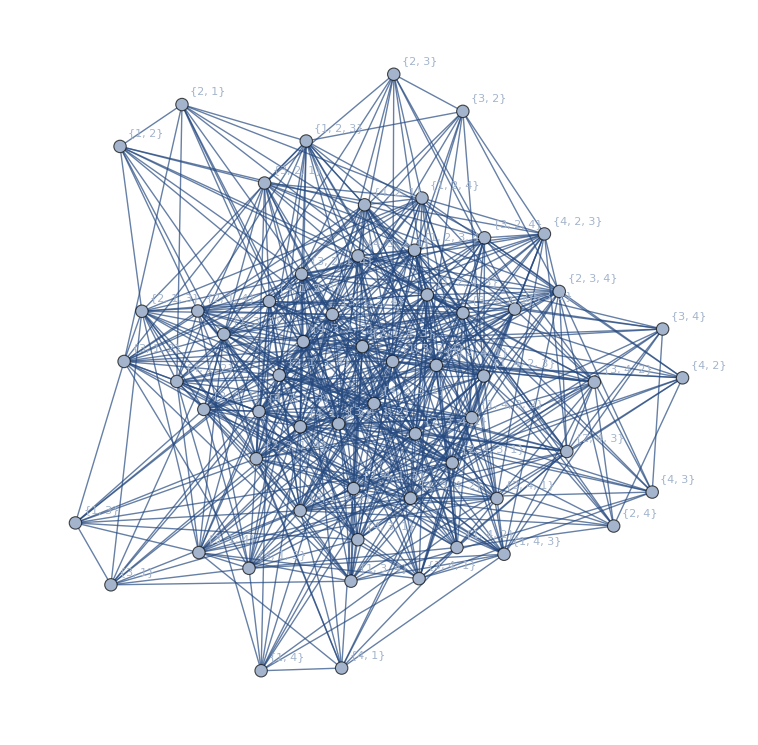

```mathematica
n=4;
ps=Sort[Join[Flatten[Table[FindPath[CompleteGraph[n],i,j,∞,All],{i,1,n-1},{j,i+1,n}],2],Flatten[Table[FindPath[CompleteGraph[n],j,i,∞,All],{i,1,n-1},{j,i+1,n}],2]]];
(*Join[Flatten[Table[If[InterSubpathQ[ps[[i]],ps[[j]]],{i->j},{}],{i,1,Length[ps]-1},{j,i+1,Length[ps]}]],*)Join[{},Flatten[Table[If[ContradictingPathsQ[ps[[i]],ps[[j]]],{j<->i},{}],{i,1,Length[ps]-1},{j,i+1,Length[ps]}]]]
Graph[Table[Labeled[i,ToString[ps[[i]]]],{i,1,Length[ps]}],%]
(*Flatten[Table[If[SubpathQ[ps[[i]],ps[[j]]],{i->j},{}],{i,1,Length[ps]-1},{j,i+1,Length[ps]}]];
gwuh=Graph[%](*Graph[Table[Labeled[i,ToString[ps[[i]]]],{i,1,Length[ps]}],%]*)
ghuh=UndirectedGraph[gwuh]*)
```

```mathematica
AdjacencyMatrix[%]
```

SparseArray[<1212>, {60, 60}]

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
Path exists⇒ Subpath exists
Path exists⇒ Intersubpath exists
Want
```

```mathematica
VertexDegree[%]
```

{18,18,18,18,18,18,18,18,18,18,18,18,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

{147,148,149,150,499,500,501,502,503,504,505,506,507,508,509,510,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950}

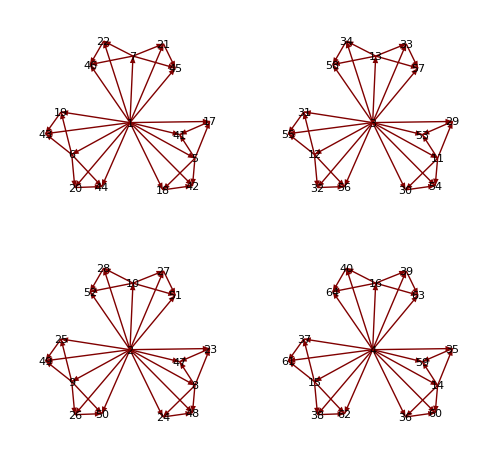

```mathematica
Complement[Sort[First[ConnectedComponents[ghuh]]],{30}]
GraphPlot[Subgraph[gwuh,%],VertexLabeling->True]
```

```mathematica
EdgeCount[ghuh]
```

1800

```mathematica
VertexCount[ghuh]
```

320

```mathematica
VertexDegree[ghuh]
```

{48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}

```mathematica
VertexConnectivity[ghuh]
```

7

```mathematica
EdgeConnectivity[ghuh]
```

7

```mathematica
Select[GraphData[60],EdgeCount[GraphData[#]]==168&]
```

{}

```mathematica
AdjacencyMatrix[gwuh]
```

SparseArray[<1800>, {320, 320}]

```mathematica
ArrayPlot[%]
```

-Graphics-

-Graphics-

```mathematica
FindCycle[gwuh,∞,All]
```

{}

```mathematica
GraphPlot3D[gwuh,VertexLabeling->True]
```

-Graphics3D-